```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_BITW100/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW100 Price | % Change | log return future | log return BITW100
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 56673.5 | 3.95% | 0.0212907 | 0.0387287
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 54520.6 | -17.93% | -0.0904653 | -0.19761
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 66432.6 | -0.15% | -0.0196938 | -0.00146147
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 66529.8 | -1.50% | -0.131645 | -0.119384
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 74965.9 | 7.82% | 0.03685 | 0.0753035
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 69528.1 | -10.74% | -0.119603 | -0.113618
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 77894. | -2.67% | -0.042369 | -0.0270599
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 80030.6 | 3.17% | 0.018947 | 0.0312522
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 77568.1 | -2.89% | -0.0359909 | -0.0180946)

```mathematica
Dimensions[data]
```

{301,8}

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,8]]
```

log return BITW100

```mathematica
data[[1,7]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
{α0=3.4244905596295756,β0=.07826356293842252`}
```

{3.42449,0.0782636}

```mathematica
{α0, β0}
```

{2.78223,0.0934428}

```mathematica
For[kk=79, kk≥70, kk--,
Print[kk];
SeedRandom[123456];
data =   
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,7;;8⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

79

78

77

76

75

74

73

72

71

70

```mathematica
{α0,β0}
```

{3.42449,0.0782636}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_BITW100/

```mathematica
For[kk=0, kk≤80, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,8⟧;
rf=data2⟦2;;All,7⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0712102 and 0.000102045 for the integral and error estimates.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0699757 and 0.00010401 for the integral and error estimates.

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0702274 and 0.000106952 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.905506 | 0.695398 | 0.758638 | 0.57019 | 0.695405 | 0.7291
 | 2021-05-13 | 0.9122 | 0.73678 | 0.777927 | 0.648624 | 0.736584 | 0.72923
 | 2021-05-06 | 0.911763 | 0.741336 | 0.763375 | 0.65719 | 0.73032 | 0.728658
 | 2021-04-29 | 0.915782 | 0.748014 | 0.771636 | 0.663125 | 0.734958 | 0.738523
 | 2021-04-22 | 0.9147 | 0.7474 | 0.767594 | 0.666605 | 0.734651 | 0.73575
 | 2021-04-15 | 0.913323 | 0.747946 | 0.762008 | 0.665893 | 0.728222 | 0.7362
 | 2021-04-08 | 0.912949 | 0.745586 | 0.762008 | 0.664844 | 0.726643 | 0.73668
 | 2021-04-01 | 0.917132 | 0.753932 | 0.765237 | 0.672376 | 0.73432 | 0.748852
 | 2021-03-25 | 0.918038 | 0.754566 | 0.767875 | 0.673727 | 0.736145 | 0.749471
 | 2021-03-18 | 0.919115 | 0.755223 | 0.782515 | 0.665918 | 0.737083 | 0.758294
 | 2021-03-11 | 0.921404 | 0.764027 | 0.784914 | 0.67043 | 0.740606 | 0.763464
 | 2021-03-04 | 0.921464 | 0.758061 | 0.783729 | 0.672531 | 0.74125 | 0.759656
 | 2021-02-25 | 0.914948 | 0.75019 | 0.756939 | 0.666016 | 0.727159 | 0.745608
 | 2021-02-18 | 0.916947 | 0.757091 | 0.772101 | 0.680287 | 0.728463 | 0.75245
 | 2021-02-10 | 0.923675 | 0.768529 | 0.784893 | 0.690144 | 0.739018 | 0.766158
 | 2021-02-03 | 0.925949 | 0.773897 | 0.79214 | 0.693611 | 0.747137 | 0.769308
 | 2021-01-27 | 0.929272 | 0.780794 | 0.802797 | 0.695758 | 0.752071 | 0.777408
 | 2021-01-20 | 0.924149 | 0.791117 | 0.83359 | 0.684405 | 0.753748 | 0.789208
 | 2021-01-12 | 0.926661 | 0.782367 | 0.797465 | 0.694615 | 0.743402 | 0.781069
 | 2021-01-05 | 0.925099 | 0.771969 | 0.78433 | 0.706401 | 0.732432 | 0.780784
 | 2020-12-28 | 0.921175 | 0.754241 | 0.768634 | 0.693172 | 0.719995 | 0.76627
 | 2020-12-18 | 0.92491 | 0.770236 | 0.778758 | 0.705388 | 0.732099 | 0.767986
 | 2020-12-11 | 0.927544 | 0.780432 | 0.803124 | 0.710076 | 0.744054 | 0.774847
 | 2020-12-04 | 0.924242 | 0.771701 | 0.781345 | 0.707804 | 0.735893 | 0.763477
 | 2020-11-27 | 0.922636 | 0.790965 | 0.776919 | 0.708359 | 0.739667 | 0.743877
 | 2020-11-19 | 0.932825 | 0.817362 | 0.801068 | 0.739668 | 0.759429 | 0.771367
 | 2020-11-12 | 0.936823 | 0.831468 | 0.823313 | 0.740795 | 0.771726 | 0.788452
 | 2020-11-05 | 0.931797 | 0.820778 | 0.794657 | 0.736566 | 0.75527 | 0.770443
 | 2020-10-29 | 0.941019 | 0.83876 | 0.829636 | 0.758012 | 0.779024 | 0.795445
 | 2020-10-22 | 0.933899 | 0.816483 | 0.787723 | 0.736789 | 0.754378 | 0.766694
 | 2020-10-15 | 0.934747 | 0.817362 | 0.793349 | 0.737805 | 0.757963 | 0.764237
 | 2020-10-08 | 0.933947 | 0.815045 | 0.78688 | 0.733515 | 0.752129 | 0.769531
 | 2020-10-01 | 0.933769 | 0.812978 | 0.784935 | 0.73318 | 0.750522 | 0.771366
 | 2020-09-24 | 0.934424 | 0.814859 | 0.786686 | 0.734631 | 0.751687 | 0.768209
 | 2020-09-17 | 0.93483 | 0.805242 | 0.786236 | 0.733343 | 0.756822 | 0.765164
 | 2020-09-10 | 0.939888 | 0.807779 | 0.783814 | 0.745483 | 0.76106 | 0.779443
 | 2020-09-02 | 0.947293 | 0.841483 | 0.842993 | 0.753894 | 0.811007 | 0.81052
 | 2020-08-26 | 0.943994 | 0.801935 | 0.775407 | 0.747657 | 0.770701 | 0.79022
 | 2020-08-19 | 0.939992 | 0.788701 | 0.762943 | 0.745091 | 0.760845 | 0.781995
 | 2020-08-12 | 0.942275 | 0.800983 | 0.777619 | 0.740119 | 0.769836 | 0.790245
 | 2020-08-05 | 0.941908 | 0.792919 | 0.776172 | 0.737711 | 0.772061 | 0.78772
 | 2020-07-29 | 0.944269 | 0.788135 | 0.756014 | 0.758794 | 0.7695 | 0.786733
 | 2020-07-22 | 0.94807 | 0.793928 | 0.798745 | 0.759855 | 0.782233 | 0.794605
 | 2020-07-15 | 0.945543 | 0.796786 | 0.801562 | 0.734795 | 0.778723 | 0.802771
 | 2020-07-08 | 0.943959 | 0.796256 | 0.80449 | 0.729008 | 0.77698 | 0.804501
 | 2020-06-30 | 0.943987 | 0.78275 | 0.803293 | 0.730247 | 0.770921 | 0.800077
 | 2020-06-23 | 0.941711 | 0.775904 | 0.795402 | 0.724102 | 0.764978 | 0.794808
 | 2020-06-16 | 0.940222 | 0.769377 | 0.777249 | 0.729745 | 0.756304 | 0.78758
 | 2020-06-09 | 0.939524 | 0.768777 | 0.775695 | 0.720756 | 0.752878 | 0.789788
 | 2020-06-02 | 0.941397 | 0.763137 | 0.775274 | 0.727989 | 0.7527 | 0.791226
 | 2020-05-26 | 0.940766 | 0.762808 | 0.771217 | 0.726806 | 0.751916 | 0.789846
 | 2020-05-18 | 0.938015 | 0.758067 | 0.772306 | 0.721031 | 0.747148 | 0.78575
 | 2020-05-11 | 0.936255 | 0.757705 | 0.765947 | 0.717273 | 0.745516 | 0.781714
 | 2020-05-04 | 0.935204 | 0.75434 | 0.770865 | 0.717218 | 0.739537 | 0.78023
 | 2020-04-27 | 0.937183 | 0.762299 | 0.77056 | 0.725949 | 0.747471 | 0.780554
 | 2020-04-20 | 0.93587 | 0.761237 | 0.77085 | 0.722863 | 0.744524 | 0.777739
 | 2020-04-13 | 0.932218 | 0.755025 | 0.761487 | 0.722563 | 0.739285 | 0.769386
 | 2020-04-03 | 0.93264 | 0.753365 | 0.749697 | 0.732983 | 0.736966 | 0.772101
 | 2020-03-27 | 0.931937 | 0.752928 | 0.769705 | 0.712436 | 0.737088 | 0.774635
 | 2020-03-20 | 0.930793 | 0.753329 | 0.768947 | 0.710677 | 0.735967 | 0.772338
 | 2020-03-13 | 0.928344 | 0.768992 | 0.770865 | 0.705484 | 0.740922 | 0.765667
 | 2020-03-06 | 0.932039 | 0.786398 | 0.777327 | 0.688598 | 0.734466 | 0.792565
 | 2020-02-28 | 0.931154 | 0.762274 | 0.725014 | 0.709518 | 0.716174 | 0.773724
 | 2020-02-21 | 0.933017 | 0.76764 | 0.724906 | 0.713143 | 0.719879 | 0.776519
 | 2020-02-13 | 0.934185 | 0.76911 | 0.75758 | 0.717571 | 0.724675 | 0.777002
 | 2020-02-06 | 0.936302 | 0.785445 | 0.80521 | 0.691594 | 0.740944 | 0.800014
 | 2020-01-30 | 0.941617 | 0.768531 | 0.752754 | 0.732241 | 0.745832 | 0.78713
 | 2020-01-23 | 0.940812 | 0.766041 | 0.794236 | 0.682058 | 0.755655 | 0.78828
 | 2020-01-15 | 0.936762 | 0.753947 | 0.76845 | 0.681239 | 0.742379 | 0.773763
 | 2020-01-08 | 0.934492 | 0.765158 | 0.795283 | 0.664211 | 0.749906 | 0.784789
 | 2019-12-31 | 0.928827 | 0.728163 | 0.74998 | 0.673181 | 0.727277 | 0.759528
 | 2019-12-23 | 0.927355 | 0.739173 | 0.77942 | 0.646759 | 0.733798 | 0.768337
 | 2019-12-16 | 0.926098 | 0.731044 | 0.76494 | 0.647008 | 0.724482 | 0.761163
 | 2019-12-09 | 0.92569 | 0.728029 | 0.763103 | 0.645519 | 0.723857 | 0.762325
 | 2019-12-02 | 0.922918 | 0.735889 | 0.779341 | 0.64138 | 0.729318 | 0.759189
 | 2019-11-22 | 0.919959 | 0.722686 | 0.760027 | 0.636345 | 0.71701 | 0.744279
 | 2019-11-15 | 0.91767 | 0.723661 | 0.766296 | 0.630296 | 0.7182 | 0.744633
 | 2019-11-08 | 0.915912 | 0.7127 | 0.727078 | 0.666868 | 0.705207 | 0.72986
 | 2019-11-01 | 0.91798 | 0.713893 | 0.730962 | 0.667624 | 0.708555 | 0.734618
 | 2019-10-25 | 0.917657 | 0.711878 | 0.739693 | 0.653395 | 0.705968 | 0.736551
 | 2019-10-18 | 0.91312 | 0.71497 | 0.718289 | 0.677151 | 0.704476 | 0.723298

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.908445 | 0.747848 | 0.69713 | 0.731824 | 0.707608 | 0.610533
 | 2021-05-13 | 0.710758 | 0.399058 | 0.43028 | 0.396471 | 0.436482 | 0.461538
 | 2021-05-06 | 0.970866 | 0.919017 | 0.954336 | 0.914958 | 0.949968 | 0.448273
 | 2021-04-29 | 0.733344 | 0.765576 | 0.626557 | 0.828637 | 0.5727 | 0.364961
 | 2021-04-22 | 0.909907 | 0.60873 | 0.651309 | 0.595632 | 0.651309 | 0.748643
 | 2021-04-15 | 0.960507 | 0.893334 | 0.96475 | 0.883984 | 0.96475 | -0.104652
 | 2021-04-08 | 0.932219 | 1.33688 | 1.27236 | 1.3427 | 1.27216 | 0.657102
 | 2021-04-01 | 0.860212 | 0.764718 | 0.790142 | 0.741091 | 0.807081 | 0.397038
 | 2021-03-25 | 0.958621 | 1.28066 | 0.953869 | 1.33738 | 0.729949 | 0.815525
 | 2021-03-18 | 0.937121 | 0.788353 | 0.791976 | 0.785078 | 0.793063 | 0.52903
 | 2021-03-11 | 0.831093 | 0.468866 | 0.499775 | 0.464478 | 0.505459 | 0.669383
 | 2021-03-04 | 0.713077 | 2.15329 | 2.25727 | 2.09179 | 2.28071 | 0.830479
 | 2021-02-25 | 0.974906 | 0.723268 | 0.757353 | 0.713684 | 0.776703 | 0.881438
 | 2021-02-18 | 0.981226 | 0.838737 | 0.858548 | 0.822855 | 0.89382 | 0.860458
 | 2021-02-10 | 0.598601 | -20.5776 | -21.1572 | -19.9166 | -21.4758 | 0.659955
 | 2021-02-03 | 0.852127 | 0.155579 | 0.104844 | 0.324447 | -0.00921251 | 0.811144
 | 2021-01-27 | 0.698171 | -1.87292 | -1.71375 | -1.40781 | -2.20998 | 0.704321
 | 2021-01-20 | 0.972316 | 0.992405 | 0.971151 | 0.912094 | 0.98585 | 0.593331
 | 2021-01-12 | 0.935993 | 1.00047 | 0.96043 | 1.00466 | 0.933568 | 0.504356
 | 2021-01-05 | 0.972127 | 0.865649 | 0.865973 | 0.865545 | 0.867022 | 0.747738
 | 2020-12-28 | 0.908204 | 6.51201 | 8.57294 | 6.12517 | 9.97539 | 0.784858
 | 2020-12-18 | 0.960343 | 0.0901378 | 0.0943211 | 0.0898902 | 0.0961569 | 0.94777
 | 2020-12-11 | 0.985327 | 313.181 | 420.519 | 305.442 | 589.545 | 0.986688
 | 2020-12-04 | 0.793993 | 0.602413 | 0.626797 | 0.600964 | 0.642434 | -0.73702
 | 2020-11-27 | 0.989295 | 0.711748 | 0.507791 | 0.588262 | 0.535545 | 0.964298
 | 2020-11-19 | 0.859322 | 0.784707 | 0.806314 | 0.784707 | 0.835183 | -0.0089735
 | 2020-11-12 | 0.897128 | 0.34791 | 0.100545 | 0.346533 | 0.253797 | 0.809364
 | 2020-11-05 | 0.755427 | -1.1351 | -1.24774 | -1.14694 | -1.45309 | 0.707651
 | 2020-10-29 | 0.982056 | -1.99676 | -1.99003 | -1.97359 | -2.32253 | 0.997294
 | 2020-10-22 | 0.988804 | 0.749155 | 0.726062 | 0.727254 | 0.708637 | 1.07689
 | 2020-10-15 | 0.928607 | 0.308902 | 0.280473 | 0.284042 | 0.259914 | 0.920493
 | 2020-10-08 | 0.95936 | 0.687951 | 0.697933 | 0.690243 | 0.696899 | 0.852079
 | 2020-10-01 | 0.961749 | 0.621223 | 0.64154 | 0.632247 | 0.64899 | 0.910396
 | 2020-09-24 | 0.93528 | 0.715597 | 0.745559 | 0.732302 | 0.758144 | 0.650383
 | 2020-09-17 | 0.929481 | 0.637744 | 0.668496 | 0.662997 | 0.665236 | 0.846657
 | 2020-09-10 | -0.0218638 | -3.77415 | -4.031 | -3.98531 | -4.00284 | 0.494429
 | 2020-09-02 | 0.928408 | 0.697709 | 0.701456 | 0.697081 | 0.709199 | 0.710982
 | 2020-08-26 | 0.92501 | 0.790141 | 0.808732 | 0.84453 | 0.814501 | 0.518776
 | 2020-08-19 | 0.927811 | 0.834113 | 0.791326 | 0.864238 | 0.840752 | 0.598897
 | 2020-08-12 | 0.915245 | 0.654955 | 0.628603 | 0.644718 | 0.626674 | 0.686442
 | 2020-08-05 | 0.977721 | 0.934207 | 0.892411 | 0.925017 | 0.892814 | 0.7656
 | 2020-07-29 | 0.392393 | 0.497141 | 0.589782 | 0.404196 | 0.488685 | 0.0944107
 | 2020-07-22 | 0.945701 | 87.2318 | 82.5163 | 93.7781 | 76.3398 | 0.888597
 | 2020-07-15 | 0.927981 | 0.550131 | 0.56627 | 0.569581 | 0.56624 | 0.848933
 | 2020-07-08 | 0.969394 | 0.987615 | 0.952488 | 0.952185 | 0.953462 | 0.433466
 | 2020-06-30 | 0.974316 | 1.05464 | 1.07082 | 1.06582 | 1.06762 | 0.694204
 | 2020-06-23 | 0.949714 | 0.835285 | 0.824944 | 0.826108 | 0.82624 | 2.06743
 | 2020-06-16 | 0.988934 | 0.992353 | 0.942053 | 0.984832 | 0.977539 | 0.862955
 | 2020-06-09 | 0.992451 | 0.874338 | 0.893128 | 0.919875 | 0.927813 | 0.926426
 | 2020-06-02 | 0.941889 | 0.281179 | 0.345943 | 0.351903 | 0.372894 | 0.846439
 | 2020-05-26 | 0.898731 | 0.149143 | 0.339037 | 0.291354 | 0.295292 | 0.678325
 | 2020-05-18 | 0.959553 | 1.00027 | 0.955274 | 0.952 | 0.952644 | 0.394823
 | 2020-05-11 | 0.983819 | 0.81478 | 0.900246 | 0.880584 | 0.885786 | 0.846391
 | 2020-05-04 | 0.990087 | 0.882863 | 0.911839 | 0.914979 | 0.91943 | 0.881248
 | 2020-04-27 | 0.980572 | -0.0551231 | -0.0301391 | -0.0490176 | -0.0393005 | 0.932252
 | 2020-04-20 | 0.927108 | 4.54288 | 3.19259 | 3.4529 | 3.32947 | 0.851269
 | 2020-04-13 | 0.994511 | 0.865917 | 0.948107 | 0.944726 | 0.938118 | 0.923683
 | 2020-04-03 | 0.986896 | 1.00781 | 0.964421 | 0.961823 | 0.95139 | 0.851418
 | 2020-03-27 | 0.98424 | 0.575601 | 0.697129 | 0.701167 | 0.703101 | 0.915383
 | 2020-03-20 | 0.985516 | 0.769652 | 0.730464 | 0.729066 | 0.729268 | 0.940871
 | 2020-03-13 | 0.984337 | 0.706373 | 0.770486 | 0.738231 | 0.7635 | 0.986242
 | 2020-03-06 | 0.977241 | 0.837083 | 0.917471 | 0.830976 | 0.885532 | -0.197696
 | 2020-02-28 | 0.966819 | 0.706022 | 0.738499 | 0.762653 | 0.761715 | 0.828519
 | 2020-02-21 | 0.886218 | 0.71216 | 0.719471 | 0.72746 | 0.728801 | 0.305715
 | 2020-02-13 | 0.948864 | 0.814983 | 0.825434 | 0.834333 | 0.83762 | 0.697196
 | 2020-02-06 | 0.915747 | 1.2098 | 1.1243 | 1.20627 | 1.2227 | 0.603313
 | 2020-01-30 | 0.921534 | 0.698585 | 0.678979 | 0.677861 | 0.67839 | 0.7137
 | 2020-01-23 | 0.971754 | 1.18116 | 1.30444 | 1.20081 | 1.25653 | 0.921645
 | 2020-01-15 | 0.955609 | 0.778868 | 0.845291 | 0.803945 | 0.818965 | 0.685449
 | 2020-01-08 | 0.977279 | 1.00022 | 1.10034 | 0.975387 | 1.04804 | 0.819767
 | 2019-12-31 | 0.936495 | 0.302898 | 0.466387 | 0.544952 | 0.502392 | 0.79144
 | 2019-12-23 | 0.857307 | 0.757377 | 0.752539 | 0.75807 | 0.755207 | 0.279205
 | 2019-12-16 | 0.975921 | 0.693319 | 0.74409 | 0.699626 | 0.719519 | 0.959572
 | 2019-12-09 | 0.96467 | 0.784061 | 0.849559 | 0.797635 | 0.815177 | 0.663544
 | 2019-12-02 | 0.9889 | 1.01777 | 0.851093 | 0.988015 | 0.94731 | 0.854898
 | 2019-11-22 | 0.988637 | 0.880427 | 0.858422 | 0.884098 | 0.893749 | 0.935198
 | 2019-11-15 | 0.996743 | 0.912074 | 0.972393 | 0.896185 | 0.932067 | 1.46926
 | 2019-11-08 | 0.866149 | 0.881494 | 0.857954 | 0.884747 | 0.883799 | -0.332913
 | 2019-11-01 | 0.972936 | 0.969132 | 0.946728 | 0.971063 | 0.971961 | 0.665561
 | 2019-10-25 | 0.928787 | -0.4354 | -0.843376 | -0.239523 | -0.384794 | 0.850334
 | 2019-10-18 | 0.990209 | 0.824264 | 0.834465 | 0.868399 | 0.826852 | 0.945446

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

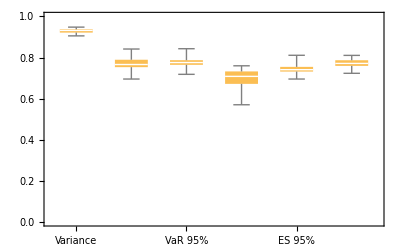

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

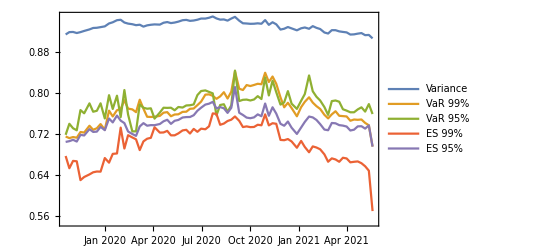

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

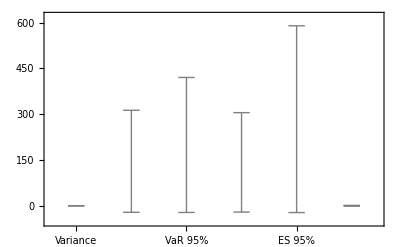

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

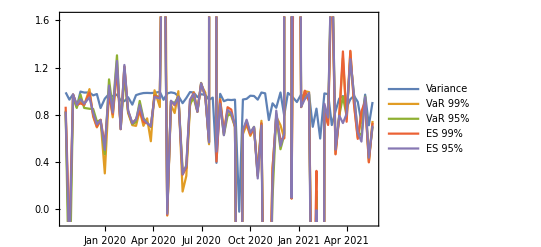

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,8]]
```

log return BITW100

```mathematica
data[[1,7]]
```

log return future

```mathematica
data[[2,2]]
```

2019-10-18 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW100 Price | % Change | log return future | log return BITW100
405 | 2019-10-18 20:00:00+00:00 | 7990. | BTCX19 Curncy | 8088.31 | -1.40% | -0.0142904 | -0.0141057
406 | 2019-10-17 20:00:00+00:00 | 8105. | BTCX19 Curncy | 8203.21 | 1.87% | 0.0142904 | 0.0185417
407 | 2019-10-16 20:00:00+00:00 | 7990. | BTCX19 Curncy | 8052.51 | -2.80% | -0.0295953 | -0.0284302
408 | 2019-10-15 20:00:00+00:00 | 8230. | BTCX19 Curncy | 8284.73 | -2.16% | -0.0222298 | -0.0218602
409 | 2019-10-14 20:00:00+00:00 | 8415. | BTCX19 Curncy | 8467.83 | -0.57% | 0. | 0.00741301
410 | 2019-10-11 20:00:00+00:00 | 8415. | BTCX19 Curncy | 8405.29 | -2.86% | -0.0275435 | -0.0290541
411 | 2019-10-10 20:00:00+00:00 | 8650. | BTCX19 Curncy | 8653.08 | -0.60% | -0.00403808 | -0.0060259
412 | 2019-10-09 20:00:00+00:00 | 8685. | BTCX19 Curncy | 8705.38 | 5.19% | 0.0544191 | 0.050567
413 | 2019-10-08 20:00:00+00:00 | 8225. | BTCX19 Curncy | 8276.12 | -0.73% | -0.00787167 | -0.00735917)

```mathematica
hvec
```

{{2019-10-18},{0.958579},{0.972054},{0.966217},{0.946799},{0.970573},{0.965119},{{0.044549538540799086, {h$203355344 -> 0.972053608732371}},{0.024200211420043395, {h$203355344 -> 0.9662165774028157}},{0.05824941853663334, {h$203355344 -> 0.9467990778257693}},{0.03718206399773098, {h$203355344 -> 0.9705726164331634}},{0.02079916894034476, {h$203355344 -> 0.9651187953015313}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

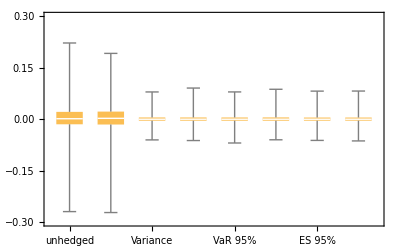

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

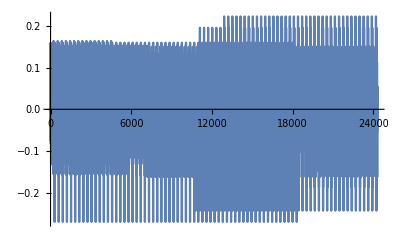

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

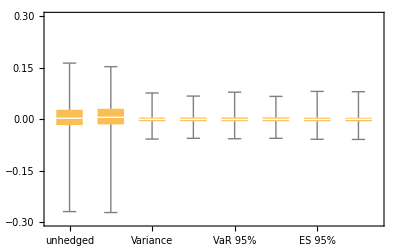

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

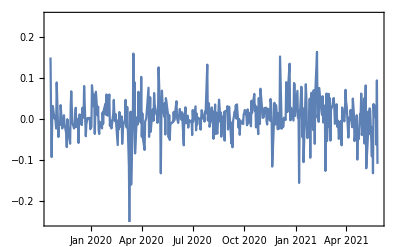
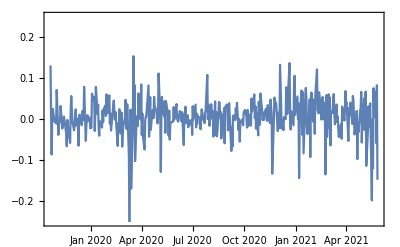

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

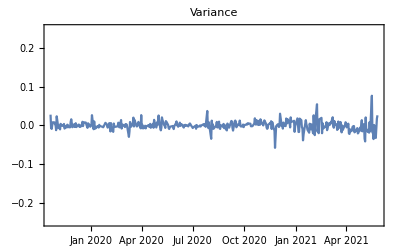
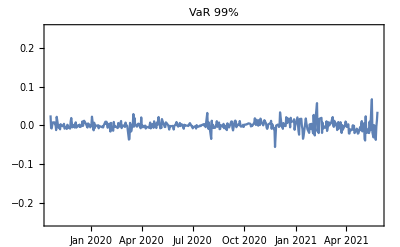
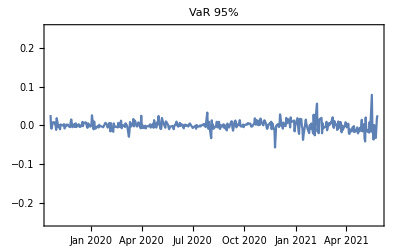
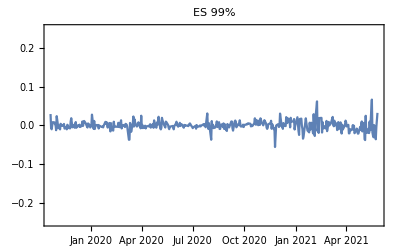
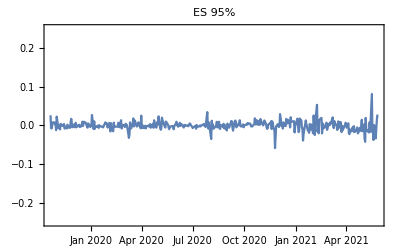
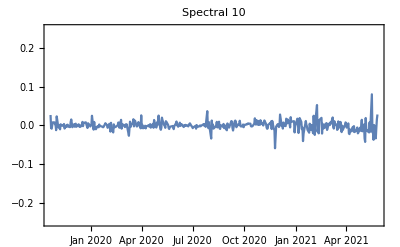

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

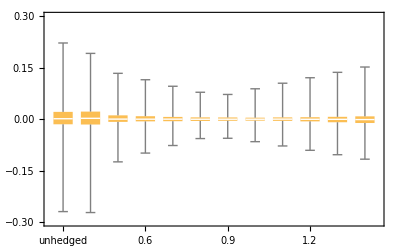

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

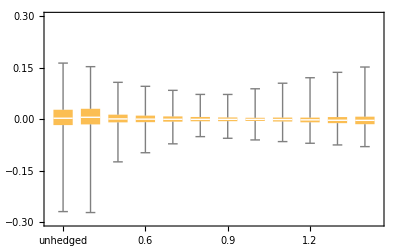

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤80, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.94396 | 1.01306 | 0.944355 | 0.991353 | 0.958549 | 0.959986
2021-05-13 | 0.925706 | 0.871693 | 0.939893 | 0.866042 | 0.953441 | 0.948035
2021-05-06 | 0.927536 | 0.873028 | 0.934074 | 0.869172 | 0.952882 | 0.957106
2021-04-29 | 0.934229 | 0.891874 | 0.935846 | 0.871927 | 0.952882 | 0.956282
2021-04-22 | 0.933677 | 0.890588 | 0.952882 | 0.871424 | 0.952882 | 0.951196
2021-04-15 | 0.934883 | 0.882345 | 0.952882 | 0.873109 | 0.952882 | 0.951825
2021-04-08 | 0.933086 | 0.879308 | 0.952882 | 0.87267 | 0.953112 | 0.951071
2021-04-01 | 0.934193 | 0.902865 | 0.932882 | 0.87497 | 0.952882 | 0.949276
2021-03-25 | 0.935121 | 0.907724 | 0.93452 | 0.875147 | 0.952882 | 0.94053
2021-03-18 | 0.938417 | 0.906746 | 0.94267 | 0.87428 | 0.953441 | 0.952991
2021-03-11 | 0.937568 | 0.885 | 0.943342 | 0.876717 | 0.954069 | 0.951958
2021-03-04 | 0.937445 | 0.901712 | 0.943923 | 0.876746 | 0.953441 | 0.970697
2021-02-25 | 0.934036 | 0.88664 | 0.928424 | 0.874892 | 0.952145 | 0.949081
2021-02-18 | 0.933154 | 0.894615 | 0.915746 | 0.877675 | 0.953368 | 0.971825
2021-02-10 | 0.936858 | 0.914438 | 0.940192 | 0.885061 | 0.954352 | 0.964868
2021-02-03 | 0.947817 | 0.923474 | 0.934541 | 0.88664 | 0.959419 | 0.964056
2021-01-27 | 0.951139 | 0.930718 | 0.916838 | 0.890159 | 0.960111 | 0.975545
2021-01-20 | 0.949201 | 0.98029 | 1.01948 | 0.895023 | 0.967399 | 0.949254
2021-01-12 | 0.951728 | 0.894737 | 0.933863 | 0.890642 | 0.960111 | 0.979751
2021-01-05 | 0.949693 | 0.898268 | 0.912581 | 0.893682 | 0.958866 | 1.01437
2020-12-28 | 0.940723 | 0.894141 | 0.929779 | 0.887452 | 0.954031 | 0.954197
2020-12-18 | 0.940946 | 0.89753 | 0.939185 | 0.895065 | 0.957464 | 0.962181
2020-12-11 | 0.94615 | 0.902323 | 0.925508 | 0.900651 | 0.958866 | 0.952429
2020-12-04 | 0.944684 | 0.898551 | 0.934922 | 0.89639 | 0.958246 | 0.949141
2020-11-27 | 0.948398 | 0.922634 | 0.961378 | 0.946091 | 0.956106 | 0.963846
2020-11-19 | 0.946574 | 0.90238 | 0.927228 | 0.90238 | 0.960425 | 0.969784
2020-11-12 | 0.948468 | 0.911592 | 0.991938 | 0.907985 | 0.953154 | 0.962871
2020-11-05 | 0.942811 | 0.906091 | 0.924336 | 0.908008 | 0.957597 | 0.955802
2020-10-29 | 0.948817 | 0.921744 | 0.918638 | 0.91105 | 0.939319 | 0.986684
2020-10-22 | 0.945636 | 0.903493 | 0.934329 | 0.932738 | 0.957597 | 0.949396
2020-10-15 | 0.944626 | 0.90238 | 0.934424 | 0.930402 | 0.957597 | 0.949215
2020-10-08 | 0.940054 | 0.901011 | 0.961571 | 0.914914 | 0.9553 | 0.953279
2020-10-01 | 0.93805 | 0.89979 | 0.93989 | 0.921549 | 0.954595 | 0.913775
2020-09-24 | 0.937001 | 0.901257 | 0.938993 | 0.922297 | 0.954843 | 0.948697
2020-09-17 | 0.936468 | 0.914036 | 0.958112 | 0.950231 | 0.95344 | 0.928087
2020-09-10 | 0.937489 | 0.898968 | 0.960148 | 0.949264 | 0.95344 | 0.917613
2020-09-02 | 0.925846 | 0.910872 | 0.915765 | 0.910053 | 0.925872 | 0.92196
2020-08-26 | 0.911013 | 0.888357 | 0.909259 | 0.949507 | 0.915744 | 0.900782
2020-08-19 | 0.906869 | 0.915252 | 0.868303 | 0.968555 | 0.922536 | 0.90503
2020-08-12 | 0.906936 | 0.955078 | 0.91665 | 0.94015 | 0.913837 | 0.911333
2020-08-05 | 0.907467 | 0.962483 | 0.913486 | 0.95171 | 0.913959 | 0.920486
2020-07-29 | 0.910005 | 0.920273 | 0.868368 | 0.972348 | 0.925011 | 0.893242
2020-07-22 | 0.917545 | 0.963839 | 0.955419 | 0.975528 | 0.944391 | 0.921855
2020-07-15 | 0.911159 | 0.890596 | 0.916723 | 0.922083 | 0.916674 | 0.928928
2020-07-08 | 0.910111 | 0.953463 | 0.919551 | 0.919259 | 0.920491 | 0.929447
2020-06-30 | 0.91103 | 0.936003 | 0.911973 | 0.919394 | 0.916715 | 0.92046
2020-06-23 | 0.909399 | 0.974114 | 0.912834 | 0.919728 | 0.920514 | 0.926966
2020-06-16 | 0.910137 | 0.962215 | 0.894839 | 0.947652 | 0.933529 | 0.911468
2020-06-09 | 0.916608 | 0.865278 | 0.883874 | 0.910343 | 0.9182 | 0.939665
2020-06-02 | 0.917985 | 0.959485 | 0.943961 | 0.942532 | 0.937501 | 0.921355
2020-05-26 | 0.917764 | 0.95874 | 0.932606 | 0.939169 | 0.938627 | 0.924349
2020-05-18 | 0.916436 | 0.987927 | 0.94349 | 0.940257 | 0.940893 | 0.918313
2020-05-11 | 0.916311 | 0.987262 | 0.93145 | 0.94429 | 0.940893 | 0.921707
2020-05-04 | 0.917527 | 0.997518 | 0.943961 | 0.938157 | 0.929932 | 0.929369
2020-04-27 | 0.922985 | 0.957147 | 0.935075 | 0.951753 | 0.943168 | 0.924627
2020-04-20 | 0.922752 | 0.990568 | 0.937757 | 0.947938 | 0.943111 | 0.929667
2020-04-13 | 0.922041 | 0.859652 | 0.941247 | 0.937891 | 0.93133 | 0.934466
2020-04-03 | 0.923098 | 0.994165 | 0.948129 | 0.945575 | 0.935319 | 0.927633
2020-03-27 | 0.924949 | 0.99354 | 0.944368 | 0.942734 | 0.941952 | 0.931299
2020-03-20 | 0.924613 | 0.994113 | 0.943497 | 0.941691 | 0.941952 | 0.932447
2020-03-13 | 0.922238 | 0.865413 | 0.943961 | 0.904443 | 0.935402 | 0.947765
2020-03-06 | 0.924312 | 0.845687 | 0.926901 | 0.839517 | 0.894634 | 0.955843
2020-02-28 | 0.927579 | 0.847494 | 0.886479 | 0.915472 | 0.914347 | 0.947987
2020-02-21 | 0.930854 | 0.858206 | 0.884445 | 0.913119 | 0.917931 | 0.94805
2020-02-13 | 0.930661 | 0.857831 | 0.885423 | 0.908917 | 0.917593 | 0.970033
2020-02-06 | 0.93409 | 0.844082 | 0.92841 | 0.832805 | 0.885239 | 0.980796
2020-01-30 | 0.938392 | 0.961553 | 0.934567 | 0.933029 | 0.933757 | 0.97004
2020-01-23 | 0.936571 | 0.847264 | 0.935694 | 0.861357 | 0.901328 | 0.965552
2020-01-15 | 0.934876 | 0.866711 | 0.940626 | 0.894617 | 0.91133 | 0.957257
2020-01-08 | 0.932556 | 0.851133 | 0.936332 | 0.830002 | 0.891824 | 0.965627
2019-12-31 | 0.931478 | 0.993036 | 0.936027 | 0.908631 | 0.923472 | 0.955715
2019-12-23 | 0.930929 | 0.855686 | 0.934808 | 0.84435 | 0.891179 | 0.959592
2019-12-16 | 0.932568 | 0.880003 | 0.944445 | 0.888008 | 0.913258 | 0.94641
2019-12-09 | 0.932462 | 0.872962 | 0.945887 | 0.888076 | 0.907606 | 0.944395
2019-12-02 | 0.934574 | 0.84162 | 0.943273 | 0.814999 | 0.889347 | 0.983762
2019-11-22 | 0.94155 | 0.883288 | 0.949253 | 0.892643 | 0.919138 | 0.949347
2019-11-15 | 0.942189 | 0.884846 | 1.03109 | 0.869432 | 0.904242 | 0.977069
2019-11-08 | 0.944379 | 0.888009 | 1.00132 | 0.937932 | 0.940176 | 0.957922
2019-11-01 | 0.947225 | 0.973592 | 0.998544 | 0.942092 | 0.944386 | 0.982604
2019-10-25 | 0.949385 | 0.96743 | 1.01661 | 0.94382 | 0.96133 | 0.95142
2019-10-18 | 0.958579 | 0.972054 | 0.966217 | 0.946799 | 0.970573 | 0.965119)

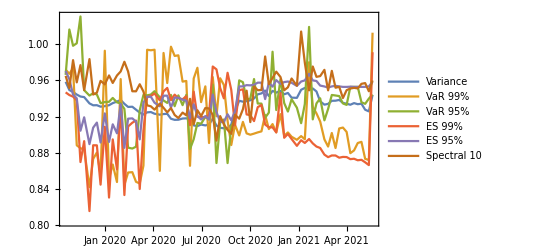

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```